{0.212207,0.31831,0.31831,0.212207}

{2.59878×10^-17,0.551329,0.551329,2.59878×10^-17}

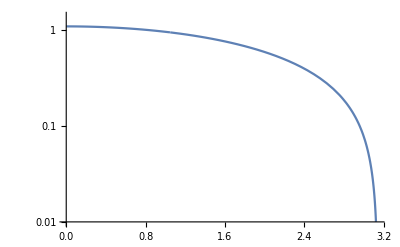

```mathematica
h0 = {0,0,0,0};
h1 = LeastSquaresFilterKernel[{"Lowpass",Pi/3},4]
h2 =  LeastSquaresFilterKernel[{"Lowpass",2Pi/3},4]
h3 = {1, 0, 0, 0};
LogPlot[Abs[ListFourierSequenceTransform[0.0h0+0.0h1+1.0h2, x]], {x, 0, Pi}, PlotRange->{10^-2, 1.4}]
```

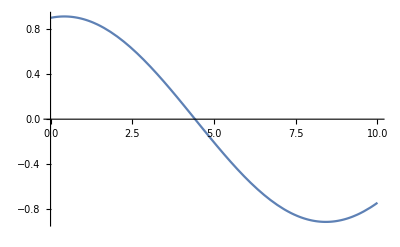

```mathematica
w = Pi/8;
Plot[h[[1]]*Cos[w*x] +h[[2]]*Cos[w (x-1)] +  h[[3]]*Cos[w(x-2)] + h[[4]]*Cos[w (x-3)], {x, 0, 10}]
```